```mathematica
(* ====================================================== *)
(* GitHub: https://github.com/yuriphestos/gradphestos-epp *)
(* Graduate Level Elementary Particle Physics             *)
(* Random Tasks for Fun                                   *)
(* ====================================================== *)
(* Task 1                                                 *)
(* Task 1.6: e+e- -> W+W- Pair Production                  *)
(* ====================================================== *)
```

```mathematica
(* Start FeynCalc *)
<< FeynCalc`
```

FeynCalc 10.2.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

#### (* e^+e^--> W^+W^- *)

```mathematica
(* Z-ff Vertex *)
ZF[μ_]:=GA[μ].(gv-ga*GA5)

ZF[μ]

(* Triple Gauge Vertex *)
TGV[μ_,ν_,λ_,p3_,p4_,q1_]:=MetricTensor[μ,ν].FV[p3-p4,λ]+MetricTensor[λ,ν].FV[-q1-p3,μ]+MetricTensor[λ,μ].FV[q1+p4,ν]

TGV[μ,ν,λ,p3,p4,q1]
```

(γ̄)^μ.(gv-ga (γ̄)^5)

(ḡ)^μν.(OverBar[p3]-OverBar[p4])^λ+(ḡ)^λν.(-OverBar[p3]-OverBar[q1])^μ+(ḡ)^λμ.(OverBar[p4]+OverBar[q1])^ν

```mathematica
q1=p1+p2;
q2=p1-p3;
```

```mathematica
(* Couplings *)
Mγcp=-e^2/ScalarProduct[q1,q1]
MZcp=gW/(2*cosw)*gWWZ/(ScalarProduct[q1,q1]-mZ^2)
Mνcp= -gW^2/(4*ScalarProduct[q2,q2])
```

-e^2/(OverBar[p1]+OverBar[p2])^2

(gW gWWZ)/(2 cosw ((OverBar[p1]+OverBar[p2])^2-mZ^2))

-gW^2/(4 (OverBar[p1]-OverBar[p3])^2)

```mathematica
(* Mγ^2 *)
FCClearScalarProducts[]
SP[p3,p3]=mW^2;
SP[p4,p4]=mW^2;

SpinorVBar[p2,0].GA[λ].SpinorU[p1,0].TGV[μ,ν,λ,p3,p4,q1].Pair[LorentzIndex[μ],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[ν],Momentum[Polarization[p3,-ⅈ]]];
%ComplexConjugate[%];
DoPolarizationSums[%,p3];
DoPolarizationSums[%,p4];
FermionSpinSum[%,ExtraFactor->1/4];

Mγsq=Mγcp^2*Simplify[DiracSimplify[%]]
```

1/(mW^4 (OverBar[p1]+OverBar[p2])^4)e^4 (-4 mW^4 (OverBar[p1]·OverBar[p2])^2+2 (mW^2 OverBar[p1]^2 ((OverBar[p2]·OverBar[p3])^2+(OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4]-mW^2)+(OverBar[p2]·OverBar[p4]) (OverBar[p2]·OverBar[p4]+OverBar[p3]·OverBar[p4]-mW^2)-2 mW^2 OverBar[p2]^2)+(OverBar[p1]·OverBar[p3])^2 (mW^2 OverBar[p2]^2-(OverBar[p2]·OverBar[p4])^2)+(OverBar[p1]·OverBar[p4]) (-(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])^2+mW^4 (OverBar[p2]·OverBar[p4])+mW^2 OverBar[p2]^2 (OverBar[p1]·OverBar[p4]+OverBar[p3]·OverBar[p4]-mW^2)+(OverBar[p2]·OverBar[p3]) (2 mW^2 (OverBar[p3]·OverBar[p4])-3 mW^4))+(OverBar[p1]·OverBar[p3]) ((OverBar[p2]·OverBar[p3]) (2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+mW^4)+mW^2 (OverBar[p2]·OverBar[p4]) (2 (OverBar[p3]·OverBar[p4])-3 mW^2)+OverBar[p2]^2 (mW^2 (OverBar[p3]·OverBar[p4])-mW^4)))+(OverBar[p1]·OverBar[p2]) (mW^2 (OverBar[p1]·OverBar[p3])^2+mW^2 (OverBar[p1]·OverBar[p4])^2+mW^2 (OverBar[p2]·OverBar[p3])^2+mW^2 (OverBar[p2]·OverBar[p4])^2-4 mW^4 (OverBar[p1]·OverBar[p4])-4 mW^4 OverBar[p1]^2-4 mW^4 (OverBar[p2]·OverBar[p3])-4 mW^4 (OverBar[p2]·OverBar[p4])-4 mW^4 OverBar[p2]^2+6 mW^4 (OverBar[p3]·OverBar[p4])-2 mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+4 mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+4 mW^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 mW^2 (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+(OverBar[p1]·OverBar[p3]) (2 (OverBar[p3]·OverBar[p4]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+2 mW^2)-2 mW^2 (OverBar[p2]·OverBar[p3])-4 mW^4)+2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+2 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])-6 mW^6))

```mathematica
(* MZ^2 *)
SpinorVBar[p2,0].ZF[λ].SpinorU[p1,0].TGV[μ,ν,λ,p3,p4,q1].Pair[LorentzIndex[μ],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[ν],Momentum[Polarization[p3,-ⅈ]]];
%ComplexConjugate[%];
DoPolarizationSums[%,p3];
DoPolarizationSums[%,p4];
FermionSpinSum[%,ExtraFactor->1/4];

MZsq=MZcp^2*Simplify[DiracSimplify[%]]
```

-1/(4 cosw^2 mW^4 ((OverBar[p1]+OverBar[p2])^2-mZ^2)^2)gW^2 gWWZ^2 (ga^2+gv^2) (4 mW^4 (OverBar[p1]·OverBar[p2])^2+2 (mW^2 OverBar[p1]^2 (-(OverBar[p2]·OverBar[p3])^2+(OverBar[p2]·OverBar[p3]) (mW^2-OverBar[p3]·OverBar[p4])-(OverBar[p2]·OverBar[p4]) (OverBar[p2]·OverBar[p4]+OverBar[p3]·OverBar[p4]-mW^2)+2 mW^2 OverBar[p2]^2)+(OverBar[p1]·OverBar[p3])^2 ((OverBar[p2]·OverBar[p4])^2-mW^2 OverBar[p2]^2)-(OverBar[p1]·OverBar[p4]) (-(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])^2+mW^4 (OverBar[p2]·OverBar[p4])+mW^2 OverBar[p2]^2 (OverBar[p1]·OverBar[p4]+OverBar[p3]·OverBar[p4]-mW^2)+(OverBar[p2]·OverBar[p3]) (2 mW^2 (OverBar[p3]·OverBar[p4])-3 mW^4))+(OverBar[p1]·OverBar[p3]) (-(OverBar[p2]·OverBar[p3]) (2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+mW^4)+mW^2 (OverBar[p2]·OverBar[p4]) (3 mW^2-2 (OverBar[p3]·OverBar[p4]))+OverBar[p2]^2 (mW^4-mW^2 (OverBar[p3]·OverBar[p4]))))+(OverBar[p1]·OverBar[p2]) (-mW^2 (OverBar[p1]·OverBar[p3])^2-mW^2 (OverBar[p1]·OverBar[p4])^2-mW^2 (OverBar[p2]·OverBar[p3])^2-mW^2 (OverBar[p2]·OverBar[p4])^2+4 mW^4 (OverBar[p1]·OverBar[p4])+4 mW^4 OverBar[p1]^2+4 mW^4 (OverBar[p2]·OverBar[p3])+4 mW^4 (OverBar[p2]·OverBar[p4])+4 mW^4 OverBar[p2]^2-6 mW^4 (OverBar[p3]·OverBar[p4])+2 mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])-4 mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p3]·OverBar[p4])-4 mW^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 mW^2 (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+2 (OverBar[p1]·OverBar[p3]) (-(OverBar[p3]·OverBar[p4]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+2 mW^2)+mW^2 (OverBar[p2]·OverBar[p3])+2 mW^4)-2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-2 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+6 mW^6))

```mathematica
(* Mν^2 *)
SpinorVBar[p2,0].GA[μ].GS[q2].GA[ν].(1-GA5).SpinorU[p1,0].Pair[LorentzIndex[μ],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[ν],Momentum[Polarization[p3,-ⅈ]]];
%ComplexConjugate[%];
FermionSpinSum[%,ExtraFactor->1/4];
DoPolarizationSums[%,p3];
DoPolarizationSums[%,p4];

Mνsq=Mνcp^2*Simplify[DiracSimplify[%]]
```

-1/(8 mW^4 (OverBar[p1]-OverBar[p3])^4)gW^4 ((OverBar[p1]·OverBar[p2]) (-4 mW^2 (OverBar[p1]·OverBar[p3])^2+4 mW^4 (OverBar[p1]·OverBar[p3])-mW^4 OverBar[p1]^2+mW^6)-8 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4]) (OverBar[p1]·OverBar[p3])^2-4 mW^4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])+2 mW^4 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+8 mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])-8 mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+2 OverBar[p1]^2 ((OverBar[p2]·OverBar[p4]) (2 (OverBar[p3]·OverBar[p4]) (OverBar[p1]·OverBar[p3]+mW^2)-mW^2 (OverBar[p1]·OverBar[p4]))+mW^2 (OverBar[p2]·OverBar[p3]) (OverBar[p1]·OverBar[p3]+mW^2)))

```mathematica
(* Subscript[M, γ] Subscript[M, Z] *)
ComplexConjugate[SpinorVBar[p2,0].GA[λ].SpinorU[p1,0].TGV[μ,ν,λ,p3,p4,q1].Pair[LorentzIndex[μ],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[ν],Momentum[Polarization[p3,-ⅈ]]]].SpinorVBar[p2,0].ZF[σ].SpinorU[p1,0].TGV[α,β,σ,p3,p4,q1].Pair[LorentzIndex[α],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[β],Momentum[Polarization[p3,-ⅈ]]];
DoPolarizationSums[%,p3];
DoPolarizationSums[%,p4];
FermionSpinSum[%,ExtraFactor->1/4];

MγMZ=Mγcp*MZcp*Simplify[DiracSimplify[%]]
```

-1/(2 cosw mW^4 (OverBar[p1]+OverBar[p2])^2 ((OverBar[p1]+OverBar[p2])^2-mZ^2))e^2 gv gW gWWZ (-4 mW^4 (OverBar[p1]·OverBar[p2])^2+2 (mW^2 OverBar[p1]^2 ((OverBar[p2]·OverBar[p3])^2+(OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4]-mW^2)+(OverBar[p2]·OverBar[p4]) (OverBar[p2]·OverBar[p4]+OverBar[p3]·OverBar[p4]-mW^2)-2 mW^2 OverBar[p2]^2)+(OverBar[p1]·OverBar[p3])^2 (mW^2 OverBar[p2]^2-(OverBar[p2]·OverBar[p4])^2)+(OverBar[p1]·OverBar[p4]) (-(OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])^2+mW^4 (OverBar[p2]·OverBar[p4])+mW^2 OverBar[p2]^2 (OverBar[p1]·OverBar[p4]+OverBar[p3]·OverBar[p4]-mW^2)+(OverBar[p2]·OverBar[p3]) (2 mW^2 (OverBar[p3]·OverBar[p4])-3 mW^4))+(OverBar[p1]·OverBar[p3]) ((OverBar[p2]·OverBar[p3]) (2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+mW^4)+mW^2 (OverBar[p2]·OverBar[p4]) (2 (OverBar[p3]·OverBar[p4])-3 mW^2)+OverBar[p2]^2 (mW^2 (OverBar[p3]·OverBar[p4])-mW^4)))+(OverBar[p1]·OverBar[p2]) (mW^2 (OverBar[p1]·OverBar[p3])^2+mW^2 (OverBar[p1]·OverBar[p4])^2+mW^2 (OverBar[p2]·OverBar[p3])^2+mW^2 (OverBar[p2]·OverBar[p4])^2-4 mW^4 (OverBar[p1]·OverBar[p4])-4 mW^4 OverBar[p1]^2-4 mW^4 (OverBar[p2]·OverBar[p3])-4 mW^4 (OverBar[p2]·OverBar[p4])-4 mW^4 OverBar[p2]^2+6 mW^4 (OverBar[p3]·OverBar[p4])-2 mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+4 mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+4 mW^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 mW^2 (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+(OverBar[p1]·OverBar[p3]) (2 (OverBar[p3]·OverBar[p4]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+2 mW^2)-2 mW^2 (OverBar[p2]·OverBar[p3])-4 mW^4)+2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+2 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])-6 mW^6))

```mathematica
(* Subscript[M, Z] Subscript[M, ν] *)
ComplexConjugate[SpinorVBar[p2,0].ZF[λ].SpinorU[p1,0].TGV[μ,ν,λ,p3,p4,q1].Pair[LorentzIndex[μ],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[ν],Momentum[Polarization[p3,-ⅈ]]]].SpinorVBar[p2,0].GA[α].GS[q2].GA[β].(1-GA5).SpinorU[p1,0].Pair[LorentzIndex[α],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[β],Momentum[Polarization[p3,-ⅈ]]];
DoPolarizationSums[%,p3];
DoPolarizationSums[%,p4];
FermionSpinSum[%,ExtraFactor->1/4];

MZMν=Mνcp*MZcp*Simplify[DiracSimplify[%]]
```

1/(8 cosw mW^4 (OverBar[p1]-OverBar[p3])^2 ((OverBar[p1]+OverBar[p2])^2-mZ^2))gW^3 gWWZ (ga+gv) (2 mW^4 (OverBar[p1]·OverBar[p2])^2-mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4])^2+3 mW^2 (OverBar[p2]·OverBar[p3]) (OverBar[p1]·OverBar[p4])^2-2 mW^2 (OverBar[p2]·OverBar[p4]) (OverBar[p1]·OverBar[p3])^2+mW^2 OverBar[p1]^2 (OverBar[p2]·OverBar[p3])^2-2 mW^2 OverBar[p2]^2 (OverBar[p1]·OverBar[p3])^2-mW^2 OverBar[p1]^2 (OverBar[p2]·OverBar[p4])^2+(OverBar[p1]·OverBar[p2]) (-2 mW^2 (OverBar[p1]·OverBar[p3])^2+mW^2 ((OverBar[p1]·OverBar[p4]) (4 (OverBar[p2]·OverBar[p4])-3 (OverBar[p3]·OverBar[p4])+4 mW^2)-mW^2 (OverBar[p2]·OverBar[p3])-3 mW^2 (OverBar[p3]·OverBar[p4])-3 (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+3 mW^4)+(OverBar[p1]·OverBar[p3]) (-2 (OverBar[p3]·OverBar[p4]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+mW^2)-2 mW^2 (OverBar[p2]·OverBar[p3])+5 mW^4))+2 (OverBar[p1]·OverBar[p3])^2 (OverBar[p2]·OverBar[p4])^2+2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3]) (OverBar[p1]·OverBar[p4])^2-2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4]) (OverBar[p1]·OverBar[p3])^2+mW^4 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])+5 mW^4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+4 mW^4 OverBar[p2]^2 (OverBar[p1]·OverBar[p3])-3 mW^4 OverBar[p1]^2 (OverBar[p2]·OverBar[p3])-2 mW^4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])-3 mW^4 OverBar[p1]^2 (OverBar[p2]·OverBar[p4])-2 mW^4 OverBar[p1]^2 OverBar[p2]^2+ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (mW^2 (-3 (OverBar[p1]·OverBar[p4])+OverBar[p2]·OverBar[p4]+mW^2)-2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+mW^2))-2 mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])+mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+2 mW^2 OverBar[p1]^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])-4 mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])-mW^2 OverBar[p1]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])+3 mW^2 OverBar[p1]^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])-2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])+2 OverBar[p1]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+2 OverBar[p1]^2 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4]))

```mathematica
(* Subscript[M, γ] Subscript[M, ν] *)
ComplexConjugate[SpinorVBar[p2,0].GA[λ].SpinorU[p1,0].TGV[μ,ν,λ,p3,p4,q1].Pair[LorentzIndex[μ],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[ν],Momentum[Polarization[p3,-ⅈ]]]].SpinorVBar[p2,0].GA[α].GS[q2].GA[β].(1-GA5).SpinorU[p1,0].Pair[LorentzIndex[α],Momentum[Polarization[p4,-ⅈ]]].Pair[LorentzIndex[β],Momentum[Polarization[p3,-ⅈ]]];
DoPolarizationSums[%,p3];
DoPolarizationSums[%,p4];
FermionSpinSum[%,ExtraFactor->1/4];

MγMν=Mγcp *Mνcp*Simplify[DiracSimplify[%]]
```

1/(4 mW^4 (OverBar[p1]+OverBar[p2])^2 (OverBar[p1]-OverBar[p3])^2)e^2 gW^2 (-2 mW^4 (OverBar[p1]·OverBar[p2])^2+mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4])^2-3 mW^2 (OverBar[p2]·OverBar[p3]) (OverBar[p1]·OverBar[p4])^2+2 mW^2 (OverBar[p2]·OverBar[p4]) (OverBar[p1]·OverBar[p3])^2-mW^2 OverBar[p1]^2 (OverBar[p2]·OverBar[p3])^2+2 mW^2 OverBar[p2]^2 (OverBar[p1]·OverBar[p3])^2+mW^2 OverBar[p1]^2 (OverBar[p2]·OverBar[p4])^2+(OverBar[p1]·OverBar[p2]) (2 mW^2 (OverBar[p1]·OverBar[p3])^2+mW^2 ((OverBar[p1]·OverBar[p4]) (-4 (OverBar[p2]·OverBar[p4])+3 (OverBar[p3]·OverBar[p4])-4 mW^2)+mW^2 (OverBar[p2]·OverBar[p3])+3 mW^2 (OverBar[p3]·OverBar[p4])+3 (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])-3 mW^4)+(OverBar[p1]·OverBar[p3]) (2 (OverBar[p3]·OverBar[p4]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+mW^2)+2 mW^2 (OverBar[p2]·OverBar[p3])-5 mW^4))-2 (OverBar[p1]·OverBar[p3])^2 (OverBar[p2]·OverBar[p4])^2-2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3]) (OverBar[p1]·OverBar[p4])^2+2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4]) (OverBar[p1]·OverBar[p3])^2-mW^4 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])-5 mW^4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4])-4 mW^4 OverBar[p2]^2 (OverBar[p1]·OverBar[p3])+3 mW^4 OverBar[p1]^2 (OverBar[p2]·OverBar[p3])+2 mW^4 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])+3 mW^4 OverBar[p1]^2 (OverBar[p2]·OverBar[p4])+2 mW^4 OverBar[p1]^2 OverBar[p2]^2-ⅈ (ϵ̄)^(OverBar[p1]OverBar[p2]OverBar[p3]OverBar[p4]) (mW^2 (-3 (OverBar[p1]·OverBar[p4])+OverBar[p2]·OverBar[p4]+mW^2)-2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]+OverBar[p2]·OverBar[p4]+mW^2))+2 mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3])-mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])-mW^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])-2 mW^2 OverBar[p1]^2 (OverBar[p2]·OverBar[p3]) (OverBar[p3]·OverBar[p4])+4 mW^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])+mW^2 OverBar[p1]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p3])-3 mW^2 OverBar[p1]^2 (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p4])+2 (OverBar[p1]·OverBar[p3]) (OverBar[p1]·OverBar[p4]) (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4])-2 OverBar[p1]^2 (OverBar[p1]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4])-2 OverBar[p1]^2 (OverBar[p2]·OverBar[p3]) (OverBar[p2]·OverBar[p4]) (OverBar[p3]·OverBar[p4]))

```mathematica
(* Defining Scalar Product of Momenta *)
p=Sqrt[Ecm^2/4-mW^2];
ScalarProduct[p1,p1]=0;
ScalarProduct[p2,p2]=0;
ScalarProduct[p3,p3]=mW^2;
ScalarProduct[p4,p4]=mW^2;

ScalarProduct[p1,p2]=Ecm^2/2;
ScalarProduct[p1,p3]=Ecm/2*(Ecm/2-p*Cos[θ]);
ScalarProduct[p2,p4]=Ecm/2*(Ecm/2-p*Cos[θ]);
ScalarProduct[p1,p4]=Ecm/2*(Ecm/2+p*Cos[θ]);
ScalarProduct[p2,p3]=Ecm/2*(Ecm/2+p*Cos[θ]);
ScalarProduct[p3,p4]=Ecm^2/2-mW^2;

Pair[Momentum[p1+p2],Momentum[p1+p2]]=Ecm^2;
Pair[Momentum[p1-p3],Momentum[p1-p3]]=mW^2-2*Ecm/2*(Ecm/2-p*Cos[θ]);
Eps[Momentum[p1],Momentum[p2],Momentum[p3],Momentum[p4]]=0;
```

```mathematica
(* Total Amplitude Squared (Only γ,Z exchanges considered) *)
Msq=Mγsq+MZsq+2*(MγMZ)//FullSimplify
```

-((Ecm^2-4 mW^2) (-Ecm^4-12 Ecm^2 mW^2+(Ecm^4-4 Ecm^2 mW^2+12 mW^4) cos^2(θ)-12 mW^4) (4 cosw^2 e^4 (Ecm^2-mZ^2)^2+4 cosw e^2 Ecm^2 gv gW gWWZ (mZ^2-Ecm^2)+Ecm^4 gW^2 gWWZ^2 (ga^2+gv^2)))/(32 cosw^2 Ecm^2 mW^4 (Ecm^2-mZ^2)^2)

```mathematica
(* Msq with numerical values *)
mZ=91.18;
mW=80.37;
gv=-0.038;
ga=-0.5;
gW=0.63;
e=Sqrt[4*Pi/137];
cosw=0.88;

Msq
```

-1/(Ecm^2 (Ecm^2-8313.79)^2)9.67183×10^-10 (Ecm^2-25837.3) (-0.00772958 Ecm^2 gWWZ (8313.79-Ecm^2)+0.0997981 Ecm^4 gWWZ^2+0.0260618 (Ecm^2-8313.79)^2) (-Ecm^4-77512. Ecm^2+(Ecm^4-25837.3 Ecm^2+5.00676×10^8) cos^2(θ)-5.00676×10^8)

```mathematica
(* Total Cross-section in unit pb *)
MInt=Integrate[Msq*Sin[θ],{θ,0,π}]//FullSimplify

Subscript[σ, total]=(p*(MInt))/(16*Pi*Ecm^3)*3.89379*10^8
```

(1.28697×10^-10 (Ecm^2-25837.3) (1. Ecm^4+129187. Ecm^2+5.00676×10^8) (Ecm^4 (gWWZ (1. gWWZ+0.0774522)+0.261145)+Ecm^2 (-643.921 gWWZ-4342.21)+1.80501×10^7))/(Ecm^2 (Ecm^2-8313.79)^2)

(0.000996948 √(Ecm^2/4-6459.34) (Ecm^2-25837.3) (1. Ecm^4+129187. Ecm^2+5.00676×10^8) (Ecm^4 (gWWZ (1. gWWZ+0.0774522)+0.261145)+Ecm^2 (-643.921 gWWZ-4342.21)+1.80501×10^7))/(Ecm^5 (Ecm^2-8313.79)^2)

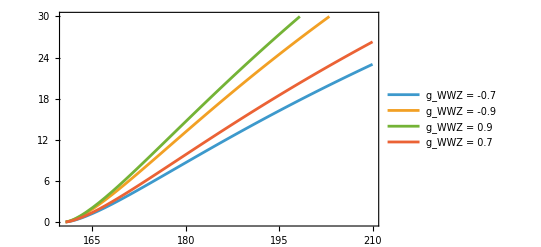
-Graphics-σ (pb)E_cm (GeV)

```mathematica
(* Final plot with gWWZ as a floating parameter *)
xsec1=Subscript[σ, total]/.{gWWZ->-0.7};
xsec2=Subscript[σ, total]/.{gWWZ->-0.9};
xsec3=Subscript[σ, total]/.{gWWZ->0.9};
xsec4=Subscript[σ, total]/.{gWWZ->0.7};

Plot[{xsec1,xsec2,xsec3,xsec4},{Ecm,160,210},Frame->True,PlotLegends->{"g_WWZ = -0.7","g_WWZ = -0.9","g_WWZ = 0.9","g_WWZ = 0.7"},PlotRange->{0,30}];
Labeled[%,{"σ (pb)","E_cm (GeV)"},{Left,Bottom}]
```